## State model

```mathematica
SetDirectory[NotebookDirectory[]];
<<State`
?stateEquations
?outEquations
?linearizeState
```

stateEquations[
	inVars_List,    (* input variable names, e.g. vS[t] *)
	stateVars_List, (* state variable names, e.g. vC1[t] *)
	equations_List  (* first-order ode and algebraic eqs, e.g. vC1'[t]==1/C1*iC1[t] *)
]
Returns the rhs of the state equations as a list.
N.b. can handle some nonlinear systems.
N.b. a common mistake is to place the prime after the argument, but it should appear before, e.g. vC2'[t].
N.b. another common mistake is to use the assignment operator '=' instead of the boolean equals '==' in equations.
N.b. the arrangement of the equations (i.e. lhs/rhs) is immaterial.
N.b. for the output equations, use the function outEquations instead.
N.b. to linearize the returned state equations, use the function linearizeState.

outEquations[
	inVars_List,    (* input variable names, e.g. vS[t] *)
	stateVars_List, (* state variable names, e.g. vC1[t] *)
	outExps_List,   (* output expressions, e.g. vR2[t]+3*vC1[t] *)
	equations_List  (* first-order ode and algebraic eqs, e.g. vC1'[t]==1/C1*iC1[t] *)
]
Returns the rhs of the output equations as a list.
N.b. can handle some nonlinear systems.
N.b. can handle any expressions in outExps as long as they are expressed in terms of variables included in the
equations list. These are *not* limited to state variables! They can be primary or secondary and expressions thereof.
N.b. a common mistake is to place the prime after the argument, but it should appear before, e.g. vC2'[t].
N.b. another common mistake is to use the assignment operator '=' instead of the boolean equals '==' in equations.
N.b. the arrangement of the equations (i.e. lhs/rhs) is immaterial.
N.b. for the state equations, use the function stateEquations instead.
N.b. to linearize the returned output equations, use the function linearizeState.

linearizeState[
	inVars_List, (* input variables *)
	inVarsOP_List, (* operating point for input variables *)
	stateVars_List, (* state variables *)
	stateVarsOP_List, (* operating point for state variables *)
	equations_List (* rhs of nonlinear (or linear) state equation *)
]
Returns an array containing the A and B matrices {A,B} of the input state equation
linearized about the input and state operating point.

```mathematica
inVars={
vs[t]
};
stateVars={
vce[t],
Tc2[t],
Tc1[t],
Tcl[t]
};
outExp=stateVars~Join~{
i1[t],
v1[t],
q2[t],
qr1[t]
};
equations={
vce'[t] == 1/ce*ice[t],
Tc1'[t] == 1/c1*qc1[t],
Tc2'[t] == 1/c2*qc2[t],
Tcl'[t] == 1/cl*qcl[t],
vrs[t]==irs[t]*rs,
vrm[t]==irm[t]*rm,
Tr1[t]==qr1[t]*r1,
Tr2[t]==qr2[t]*r2,
Tr3[t]==qr3[t]*r3,
q2[t]==v1[t]*i1[t],
T2[t]==-1/α*v1[t],
ice[t]==irs[t]-irm[t],
irm[t]==i1[t],
qc1[t]==-q2[t]-qr1[t]-qr2[t],
qc2[t]==q2[t]+qr1[t]-qr3[t],
qcl[t]==qr2[t],
vrs[t]==vs[t]-vce[t],
vrm[t]==vce[t]-v1[t],
Tr1[t]==Tc1[t]-Tc2[t],
Tr2[t]==Tc1[t]-Tcl[t],
Tr3[t]==Tc2[t],
T2[t]==Tc1[t]-Tc2[t]
};
ass={rs,r1,r2,r3,rm,cl,c1,c2,ce}//Thread[#>0]&;
n=Length[stateVars];
m=Length[outExp];
r=Length[inVars];
```

Find nonlinear state equation.

```mathematica
stateEqList=stateEquations[inVars,stateVars,equations]//Flatten;
stateEqList//Thread[D[stateVars,t]==#]&//TableForm
```

vce'[t]==-(α Tc1[t])/(ce rm)+(α Tc2[t])/(ce rm)-((rm+rs) vce[t])/(ce rm rs)+vs[t]/(ce rs)
Tc2'[t]==Tc1[t]/(c2 r1)-(α^2 Tc1[t]^2)/(c2 rm)+(-(r1 rm+r3 rm)/(c2 r1 r3 rm)+(2 α^2 Tc1[t])/(c2 rm)) Tc2[t]-(α^2 Tc2[t]^2)/(c2 rm)+(-(α Tc1[t])/(c2 rm)+(α Tc2[t])/(c2 rm)) vce[t]
Tc1'[t]==(-1/(c1 r1)-1/(c1 r2)) Tc1[t]+(α^2 Tc1[t]^2)/(c1 rm)+(1/(c1 r1)-(2 α^2 Tc1[t])/(c1 rm)) Tc2[t]+(α^2 Tc2[t]^2)/(c1 rm)+Tcl[t]/(c1 r2)+((α Tc1[t])/(c1 rm)-(α Tc2[t])/(c1 rm)) vce[t]
Tcl'[t]==Tc1[t]/(cl r2)-Tcl[t]/(cl r2)

Linearize the state equation about operating point.

```mathematica
(* symbolic operating point for state variables (can be numeric) *)
x0=stateVars/.{x_[t]:>((ToString[x]<>"0")//ToExpression)} ;
(* numeric operating point for input variables (can be symbolic) *)
u0={0}; 
dx=stateVars/.{x_[t]:>(("d"<>ToString[x[t]])//ToExpression)};
du=inVars/.{x_[t]:>(("d"<>ToString[x[t]])//ToExpression)};
ab=linearizeState[inVars,u0,stateVars,x0,stateEqList];
a=ab[[1]];b=ab[[2]];
a//MatrixForm//Print["A = ",#]&
b//MatrixForm//Print["B = ",#]&
D[dx,t]//MatrixForm//#==A.MatrixForm[dx]+B.MatrixForm[du]&
```

A = (-(rm+rs)/(ce rm rs) | α/(ce rm) | -α/(ce rm) | 0
-(Tc10 α)/(c2 rm)+(Tc20 α)/(c2 rm) | -(r1 rm+r3 rm)/(c2 r1 r3 rm)+(vce0 α)/(c2 rm)+(2 Tc10 α^2)/(c2 rm)-(2 Tc20 α^2)/(c2 rm) | 1/(c2 r1)-(vce0 α)/(c2 rm)-(2 Tc10 α^2)/(c2 rm)+(2 Tc20 α^2)/(c2 rm) | 0
(Tc10 α)/(c1 rm)-(Tc20 α)/(c1 rm) | 1/(c1 r1)-(vce0 α)/(c1 rm)-(2 Tc10 α^2)/(c1 rm)+(2 Tc20 α^2)/(c1 rm) | -1/(c1 r1)-1/(c1 r2)+(vce0 α)/(c1 rm)+(2 Tc10 α^2)/(c1 rm)-(2 Tc20 α^2)/(c1 rm) | 1/(c1 r2)
0 | 0 | 1/(cl r2) | -1/(cl r2))

B = (1/(ce rs)
0
0
0)

(dvce'[t]
dTc2'[t]
dTc1'[t]
dTcl'[t])==A.(dvce[t]
dTc2[t]
dTc1[t]
dTcl[t])+B.(dvs[t])

Find the output equation.

```mathematica
outEqList = outEquations[inVars,stateVars,outExp,equations];
Map[ToString,outExp]//Thread[#==outEqList]&//TableForm
```

vce[t]==vce[t]
Tc2[t]==Tc2[t]
Tc1[t]==Tc1[t]
Tcl[t]==Tcl[t]
i1[t]==(α Tc1[t])/rm-(α Tc2[t])/rm+vce[t]/rm
v1[t]==-α Tc1[t]+α Tc2[t]
q2[t]==-(α^2 Tc1[t]^2)/rm+(2 α^2 Tc1[t] Tc2[t])/rm-(α^2 Tc2[t]^2)/rm+(-(α Tc1[t])/rm+(α Tc2[t])/rm) vce[t]
qr1[t]==Tc1[t]/r1-Tc2[t]/r1

Linearize output equation about operating point.

```mathematica
cd=linearizeOutput[inVars,u0,stateVars,x0,outEqList];
c=cd[[1]];d=cd[[2]];
c//MatrixForm//Print["C = ",#]&
d//MatrixForm//Print["D = ",#]&
outExp//MatrixForm//#==C.MatrixForm[dx]+D.MatrixForm[du]&
```

C = (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1/rm | -α/rm | α/rm | 0
0 | α | -α | 0
-(Tc10 α)/rm+(Tc20 α)/rm | (vce0 α)/rm+(2 Tc10 α^2)/rm-(2 Tc20 α^2)/rm | -(vce0 α)/rm-(2 Tc10 α^2)/rm+(2 Tc20 α^2)/rm | 0
0 | -1/r1 | 1/r1 | 0)

D = (0
0
0
0
0
0
0
0)

(vce[t]
Tc2[t]
Tc1[t]
Tcl[t]
i1[t]
v1[t]
q2[t]
qr1[t])==C.(dvce[t]
dTc2[t]
dTc1[t]
dTcl[t])+D.(dvs[t])

Form nonlinear and linear state models for MMA.

```mathematica
nsys=NonlinearStateSpaceModel[{stateEqList,outEqList},stateVars,inVars]
sys=StateSpaceModel[{a.dx+b.du,c.dx+d.du},dx,du]
```

-(α Tc1[t])/(ce rm)+(α Tc2[t])/(ce rm)-((rm+rs) vce[t])/(ce rm rs)+vs[t]/(ce rs)Tc1[t]/(c2 r1)-(α^2 Tc1[t]^2)/(c2 rm)+(-(r1 rm+r3 rm)/(c2 r1 r3 rm)+(2 α^2 Tc1[t])/(c2 rm)) Tc2[t]-(α^2 Tc2[t]^2)/(c2 rm)+(-(α Tc1[t])/(c2 rm)+(α Tc2[t])/(c2 rm)) vce[t](-1/(c1 r1)-1/(c1 r2)) Tc1[t]+(α^2 Tc1[t]^2)/(c1 rm)+(1/(c1 r1)-(2 α^2 Tc1[t])/(c1 rm)) Tc2[t]+(α^2 Tc2[t]^2)/(c1 rm)+Tcl[t]/(c1 r2)+((α Tc1[t])/(c1 rm)-(α Tc2[t])/(c1 rm)) vce[t]Tc1[t]/(cl r2)-Tcl[t]/(cl r2)vce[t]Tc2[t]Tc1[t]Tcl[t](α Tc1[t])/rm-(α Tc2[t])/rm+vce[t]/rm-α Tc1[t]+α Tc2[t]-(α^2 Tc1[t]^2)/rm+(2 α^2 Tc1[t] Tc2[t])/rm-(α^2 Tc2[t]^2)/rm+(-(α Tc1[t])/rm+(α Tc2[t])/rm) vce[t]Tc1[t]/r1-Tc2[t]/r1vce[t]Tc2[t]Tc1[t]Tcl[t] 4188NoneNoneFalseFalseFalse{vs[t]}Automatic

-(rm+rs)/(ce rm rs)α/(ce rm)-α/(ce rm)01/(ce rs)-(Tc10 α)/(c2 rm)+(Tc20 α)/(c2 rm)-(r1 rm+r3 rm)/(c2 r1 r3 rm)+(vce0 α)/(c2 rm)+(2 Tc10 α^2)/(c2 rm)-(2 Tc20 α^2)/(c2 rm)1/(c2 r1)-(vce0 α)/(c2 rm)-(2 Tc10 α^2)/(c2 rm)+(2 Tc20 α^2)/(c2 rm)00(Tc10 α)/(c1 rm)-(Tc20 α)/(c1 rm)1/(c1 r1)-(vce0 α)/(c1 rm)-(2 Tc10 α^2)/(c1 rm)+(2 Tc20 α^2)/(c1 rm)-1/(c1 r1)-1/(c1 r2)+(vce0 α)/(c1 rm)+(2 Tc10 α^2)/(c1 rm)-(2 Tc20 α^2)/(c1 rm)1/(c1 r2)0001/(cl r2)-1/(cl r2)0100000100000100000101/rm-α/rmα/rm000α-α00-(Tc10 α)/rm+(Tc20 α)/rm(vce0 α)/rm+(2 Tc10 α^2)/rm-(2 Tc20 α^2)/rm-(vce0 α)/rm-(2 Tc10 α^2)/rm+(2 Tc20 α^2)/rm000-1/r11/r100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1841FalseFalseFalseAutomaticNone,{{dvce[t],0},{dTc2[t],0},{dTc1[t],0},{dTcl[t],0}},{{dvs[t],0}}

## Simulate

```mathematica
stateVars
```

{vce[t],Tc2[t],Tc1[t],Tcl[t]}

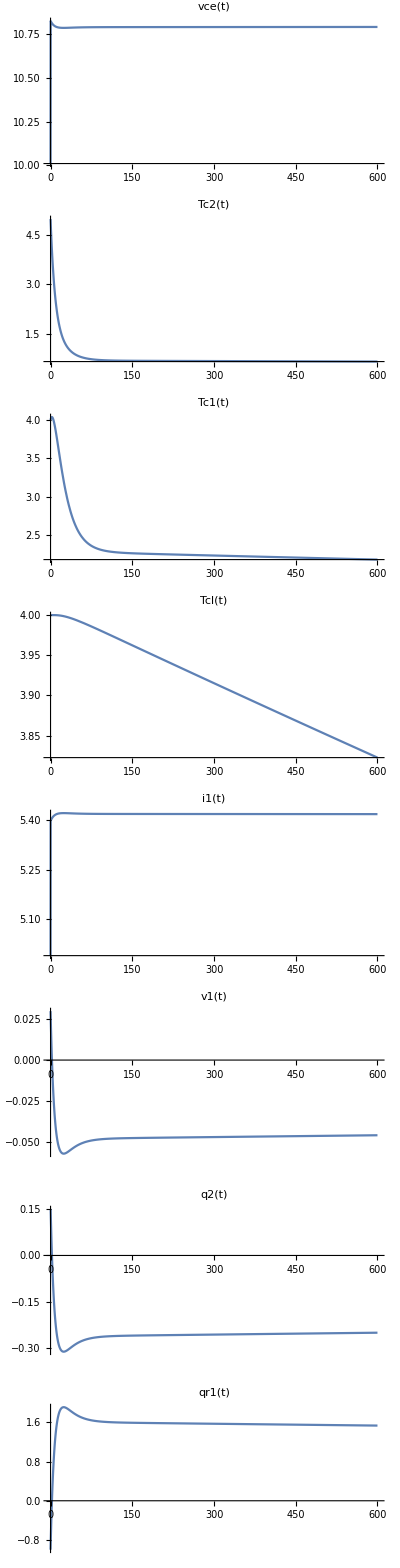

```mathematica
tlow=0;
thigh=600;
x00={10,5,4,4}; (* initial condition *)
(*sb[T_]:=1.33450*10^-2+-5.37574*10^-5*T+7.42731*10^-7*T^2+-1.27141*10^-9*T^3;*)
params={ (* these need work *)
rs->1.7,
r1->1,
r2->1.28,
r3->0.5,
rm-> 2,
cl->4.2*10^3,
c1->25,
c2->25,
ce->10*10^-4,
α->.03
};
nsysResponse=OutputResponse[{nsys/.params,x00},20*UnitStep[t],{t,tlow,thigh}];
Table[
Plot[nsysResponse[[i]],{t,tlow,thigh},PlotRange->All,PlotLabel->outExp[[i]]],
{i,1,m}
]//GraphicsColumn[#,ImageSize->Full]&
```

## Printing to Matlab (needs work)

The issue I’m having is getting Matlab to automatically generate a function file so I can ode45 it.
Once this is working, incorporate it into State as a function.

```mathematica
<<ToMatlab`
stateMatRep=Thread[stateVars->Table["x("<>ToString[i]<>")",{i,1,Length[stateVars]}]]~Join~
Thread[inVars->Table["u("<>ToString[i]<>")",{i,1,Length[inVars]}]]
myToMatlab[exp_]:=(exp/.stateMatRep//Map[ReplaceAll[#,x_[t_]:>x]&,#]&//ReplaceAll[#,α->a]&//ToMatlab//ToString);

matlabVars=stateEqList//Variables//ReplaceAll[#,α->a]&//Complement[#,stateVars~Join~inVars]&//Map[ReplaceAll[#,x_[t_]:>x]&,#]&;

(*{{"syms"}~Join~matlabVars}//Grid*)
For[i=1,i≤Length[matlabVars],i++,(matlabVars[[i]]//ToString)<>"=1; % dummy"//Print]
Length[stateVars]//Print["f=sym('f',["<>ToString[#]<>",1]);"]&;
Length[stateVars]//Print["x=sym('x',["<>ToString[#]<>",1]);"]&;
Length[inVars]//Print["u=sym('u',["<>ToString[#]<>",1]);"]&;

For[i=1,i≤Length[stateVars],i++,"f("<>ToString[i]<>")="<>(myToMatlab[stateEqList[[i]]])//Print]
```

c1=1; % dummy

c2=1; % dummy

ce=1; % dummy

cl=1; % dummy

r1=1; % dummy

r2=1; % dummy

r3=1; % dummy

rm=1; % dummy

rs=1; % dummy

2           2                           2           2                                                 2           2                                      2           2
    rm + rs      α        α            Tc10 α    Tc20 α    r1 rm + r3 rm    vce0 α   2 Tc10 α    2 Tc20 α     1     vce0 α   2 Tc10 α    2 Tc20 α        Tc10 α   Tc20 α    1     vce0 α   2 Tc10 α    2 Tc20 α       1        1     vce0 α   2 Tc10 α    2 Tc20 α     1              1        1
{{-(--------), -----, -(-----), 0}, {-(------) + ------, -(-------------) + ------ + --------- - ---------, ----- - ------ - --------- + ---------, 0}, {------ - ------, ----- - ------ - --------- + ---------, -(-----) - ----- + ------ + --------- - ---------, -----}, {0, 0, -----, -(-----)}}
    ce rm rs   ce rm    ce rm          c2 rm     c2 rm      c2 r1 r3 rm     c2 rm      c2 rm       c2 rm    c2 r1   c2 rm      c2 rm       c2 rm         c1 rm    c1 rm   c1 r1   c1 rm      c1 rm       c1 rm      c1 r1    c1 r2   c1 rm      c1 rm       c1 rm    c1 r2          cl r2    cl r2=1; % dummy

f=sym('f',[4,1]);

x=sym('x',[4,1]);

u=sym('u',[1,1]);

f(1)=[u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(2).*ce.^(-2).*rm.^(-2).*rs.^(-1) ...
  .*(rm+rs)+x(3).*ce.^(-2).*rm.^(-2).*rs.^(-1).*(rm+rs)+(-1).*x(1).* ...
  ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs),u(1).*ce.^(-1).*rs.^(-1)+( ...
  -1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs)+x(2).*ce.^(-2).* ...
  rm.^(-2).*α+(-1).*x(3).*ce.^(-2).*rm.^(-2).*α,u(1).*ce.^(-1).* ...
  rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs)+(-1).* ...
  x(2).*ce.^(-2).*rm.^(-2).*α+x(3).*ce.^(-2).*rm.^(-2).*α,u(1).* ...
  ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+ ...
  rs);u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^( ...
  -1).*(rm+rs)+x(2).*ce.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*rm.^(-1).* ...
  Tc10.*α+c2.^(-1).*rm.^(-1).*Tc20.*α)+(-1).*x(3).*ce.^(-1).*rm.^( ...
  -1).*((-1).*c2.^(-1).*rm.^(-1).*Tc10.*α+c2.^(-1).*rm.^(-1).*Tc20.* ...
  α),u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^( ...
  -1).*(rm+rs)+x(2).*ce.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*r1.^(-1).* ...
  r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+c2.^(-1).*rm.^(-1).*vce0.*α+ ...
  2.*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2)+(-1).*x(3).*ce.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*r1.^(-1).* ...
  r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+c2.^(-1).*rm.^(-1).*vce0.*α+ ...
  2.*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2),u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).* ...
  rs.^(-1).*(rm+rs)+x(2).*ce.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+( ...
  -1).*c2.^(-1).*rm.^(-1).*vce0.*α+(-2).*c2.^(-1).*rm.^(-1).*Tc10.* ...
  α.^2+2.*c2.^(-1).*rm.^(-1).*Tc20.*α.^2)+(-1).*x(3).*ce.^(-1).* ...
  rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1).*c2.^(-1).*rm.^(-1).*vce0.*α+( ...
  -2).*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2),u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).* ...
  rs.^(-1).*(rm+rs);u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).* ...
  rm.^(-1).*rs.^(-1).*(rm+rs)+x(2).*ce.^(-1).*rm.^(-1).*(c1.^(-1).* ...
  rm.^(-1).*Tc10.*α+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α)+(-1).*x(3).* ...
  ce.^(-1).*rm.^(-1).*(c1.^(-1).*rm.^(-1).*Tc10.*α+(-1).*c1.^(-1).* ...
  rm.^(-1).*Tc20.*α),u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).* ...
  rm.^(-1).*rs.^(-1).*(rm+rs)+x(2).*ce.^(-1).*rm.^(-1).*(c1.^(-1).* ...
  r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+(-2).*c1.^(-1).*rm.^( ...
  -1).*Tc10.*α.^2+2.*c1.^(-1).*rm.^(-1).*Tc20.*α.^2)+(-1).*x(3).* ...
  ce.^(-1).*rm.^(-1).*(c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).* ...
  vce0.*α+(-2).*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c1.^(-1).*rm.^(-1) ...
  .*Tc20.*α.^2),u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^( ...
  -1).*rs.^(-1).*(rm+rs)+x(2).*ce.^(-1).*rm.^(-1).*((-1).*c1.^(-1).* ...
  r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+2.* ...
  c1.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2)+(-1).*x(3).*ce.^(-1).*rm.^(-1).*((-1).*c1.^(-1).*r1.^(-1)+( ...
  -1).*c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+2.*c1.^(-1).* ...
  rm.^(-1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.*α.^2),x(2).* ...
  c1.^(-1).*ce.^(-1).*r2.^(-1).*rm.^(-1)+(-1).*x(3).*c1.^(-1).*ce.^( ...
  -1).*r2.^(-1).*rm.^(-1)+u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^( ...
  -1).*rm.^(-1).*rs.^(-1).*(rm+rs);u(1).*ce.^(-1).*rs.^(-1)+(-1).*x( ...
  1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs),u(1).*ce.^(-1).*rs.^(-1) ...
  +(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs),x(2).*ce.^(-1) ...
  .*cl.^(-1).*r2.^(-1).*rm.^(-1)+(-1).*x(3).*ce.^(-1).*cl.^(-1).* ...
  r2.^(-1).*rm.^(-1)+u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).* ...
  rm.^(-1).*rs.^(-1).*(rm+rs),(-1).*x(2).*ce.^(-1).*cl.^(-1).*r2.^( ...
  -1).*rm.^(-1)+x(3).*ce.^(-1).*cl.^(-1).*r2.^(-1).*rm.^(-1)+u(1).* ...
  ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+ ...
  rs)];

f(2)=[x(3).*c2.^(-1).*r1.^(-1)+(-1).*x(2).^2.*c2.^(-1).*ce.^(-2).*rm.^( ...
  -3).*rs.^(-2).*(rm+rs).^2+(-1).*x(3).^2.*c2.^(-1).*ce.^(-2).*rm.^( ...
  -3).*rs.^(-2).*(rm+rs).^2+x(1).*((-1).*x(2).*c2.^(-1).*ce.^(-1).* ...
  rm.^(-2).*rs.^(-1).*(rm+rs)+x(3).*c2.^(-1).*ce.^(-1).*rm.^(-2).* ...
  rs.^(-1).*(rm+rs))+x(2).*((-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(r1.*rm+r3.*rm)+2.*x(3).*c2.^(-1).*ce.^(-2).*rm.^(-3).* ...
  rs.^(-2).*(rm+rs).^2),x(3).*c2.^(-1).*r1.^(-1)+(-1).*x(2).^2.* ...
  c2.^(-1).*ce.^(-2).*rm.^(-3).*α.^2+(-1).*x(3).^2.*c2.^(-1).*ce.^( ...
  -2).*rm.^(-3).*α.^2+x(1).*(x(2).*c2.^(-1).*ce.^(-1).*rm.^(-2).*α+( ...
  -1).*x(3).*c2.^(-1).*ce.^(-1).*rm.^(-2).*α)+x(2).*((-1).*c2.^(-1) ...
  .*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+2.*x(3).*c2.^(-1) ...
  .*ce.^(-2).*rm.^(-3).*α.^2),x(3).*c2.^(-1).*r1.^(-1)+(-1).*x(2) ...
  .^2.*c2.^(-1).*ce.^(-2).*rm.^(-3).*α.^2+(-1).*x(3).^2.*c2.^(-1).* ...
  ce.^(-2).*rm.^(-3).*α.^2+x(1).*((-1).*x(2).*c2.^(-1).*ce.^(-1).* ...
  rm.^(-2).*α+x(3).*c2.^(-1).*ce.^(-1).*rm.^(-2).*α)+x(2).*((-1).* ...
  c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+2.*x(3).* ...
  c2.^(-1).*ce.^(-2).*rm.^(-3).*α.^2),x(3).*c2.^(-1).*r1.^(-1)+(-1) ...
  .*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm);x( ...
  3).*c2.^(-1).*r1.^(-1)+(-1).*x(2).^2.*c2.^(-1).*rm.^(-1).*((-1).* ...
  c2.^(-1).*rm.^(-1).*Tc10.*α+c2.^(-1).*rm.^(-1).*Tc20.*α).^2+(-1).* ...
  x(3).^2.*c2.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*rm.^(-1).*Tc10.*α+ ...
  c2.^(-1).*rm.^(-1).*Tc20.*α).^2+x(1).*(x(2).*c2.^(-1).*rm.^(-1).*( ...
  (-1).*c2.^(-1).*rm.^(-1).*Tc10.*α+c2.^(-1).*rm.^(-1).*Tc20.*α)+( ...
  -1).*x(3).*c2.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*rm.^(-1).*Tc10.*α+ ...
  c2.^(-1).*rm.^(-1).*Tc20.*α))+x(2).*((-1).*c2.^(-1).*r1.^(-1).* ...
  r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+2.*x(3).*c2.^(-1).*rm.^(-1).*( ...
  (-1).*c2.^(-1).*rm.^(-1).*Tc10.*α+c2.^(-1).*rm.^(-1).*Tc20.*α).^2) ...
  ,x(3).*c2.^(-1).*r1.^(-1)+(-1).*x(2).^2.*c2.^(-1).*rm.^(-1).*((-1) ...
  .*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+c2.^(-1) ...
  .*rm.^(-1).*vce0.*α+2.*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c2.^( ...
  -1).*rm.^(-1).*Tc20.*α.^2).^2+(-1).*x(3).^2.*c2.^(-1).*rm.^(-1).*( ...
  (-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+ ...
  c2.^(-1).*rm.^(-1).*vce0.*α+2.*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2) ...
  .*c2.^(-1).*rm.^(-1).*Tc20.*α.^2).^2+x(1).*(x(2).*c2.^(-1).*rm.^( ...
  -1).*((-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.* ...
  rm)+c2.^(-1).*rm.^(-1).*vce0.*α+2.*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+ ...
  (-2).*c2.^(-1).*rm.^(-1).*Tc20.*α.^2)+(-1).*x(3).*c2.^(-1).*rm.^( ...
  -1).*((-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.* ...
  rm)+c2.^(-1).*rm.^(-1).*vce0.*α+2.*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+ ...
  (-2).*c2.^(-1).*rm.^(-1).*Tc20.*α.^2))+x(2).*((-1).*c2.^(-1).* ...
  r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+2.*x(3).*c2.^(-1).* ...
  rm.^(-1).*((-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+ ...
  r3.*rm)+c2.^(-1).*rm.^(-1).*vce0.*α+2.*c2.^(-1).*rm.^(-1).*Tc10.* ...
  α.^2+(-2).*c2.^(-1).*rm.^(-1).*Tc20.*α.^2).^2),x(3).*c2.^(-1).* ...
  r1.^(-1)+(-1).*x(2).^2.*c2.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+( ...
  -1).*c2.^(-1).*rm.^(-1).*vce0.*α+(-2).*c2.^(-1).*rm.^(-1).*Tc10.* ...
  α.^2+2.*c2.^(-1).*rm.^(-1).*Tc20.*α.^2).^2+(-1).*x(3).^2.*c2.^(-1) ...
  .*rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1).*c2.^(-1).*rm.^(-1).*vce0.*α+ ...
  (-2).*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2).^2+x(1).*(x(2).*c2.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1) ...
  .*c2.^(-1).*rm.^(-1).*vce0.*α+(-2).*c2.^(-1).*rm.^(-1).*Tc10.* ...
  α.^2+2.*c2.^(-1).*rm.^(-1).*Tc20.*α.^2)+(-1).*x(3).*c2.^(-1).* ...
  rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1).*c2.^(-1).*rm.^(-1).*vce0.*α+( ...
  -2).*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2))+x(2).*((-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.* ...
  rm+r3.*rm)+2.*x(3).*c2.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1).* ...
  c2.^(-1).*rm.^(-1).*vce0.*α+(-2).*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+ ...
  2.*c2.^(-1).*rm.^(-1).*Tc20.*α.^2).^2),x(3).*c2.^(-1).*r1.^(-1)+( ...
  -1).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm) ...
  ;x(3).*c2.^(-1).*r1.^(-1)+(-1).*x(2).^2.*c2.^(-1).*rm.^(-1).*( ...
  c1.^(-1).*rm.^(-1).*Tc10.*α+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α).^2+ ...
  (-1).*x(3).^2.*c2.^(-1).*rm.^(-1).*(c1.^(-1).*rm.^(-1).*Tc10.*α+( ...
  -1).*c1.^(-1).*rm.^(-1).*Tc20.*α).^2+x(1).*(x(2).*c2.^(-1).*rm.^( ...
  -1).*(c1.^(-1).*rm.^(-1).*Tc10.*α+(-1).*c1.^(-1).*rm.^(-1).*Tc20.* ...
  α)+(-1).*x(3).*c2.^(-1).*rm.^(-1).*(c1.^(-1).*rm.^(-1).*Tc10.*α+( ...
  -1).*c1.^(-1).*rm.^(-1).*Tc20.*α))+x(2).*((-1).*c2.^(-1).*r1.^(-1) ...
  .*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+2.*x(3).*c2.^(-1).*rm.^(-1) ...
  .*(c1.^(-1).*rm.^(-1).*Tc10.*α+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α) ...
  .^2),x(3).*c2.^(-1).*r1.^(-1)+(-1).*x(2).^2.*c2.^(-1).*rm.^(-1).*( ...
  c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+(-2).*c1.^( ...
  -1).*rm.^(-1).*Tc10.*α.^2+2.*c1.^(-1).*rm.^(-1).*Tc20.*α.^2).^2+( ...
  -1).*x(3).^2.*c2.^(-1).*rm.^(-1).*(c1.^(-1).*r1.^(-1)+(-1).*c1.^( ...
  -1).*rm.^(-1).*vce0.*α+(-2).*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+2.* ...
  c1.^(-1).*rm.^(-1).*Tc20.*α.^2).^2+x(1).*(x(2).*c2.^(-1).*rm.^(-1) ...
  .*(c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+(-2).* ...
  c1.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c1.^(-1).*rm.^(-1).*Tc20.*α.^2)+ ...
  (-1).*x(3).*c2.^(-1).*rm.^(-1).*(c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1) ...
  .*rm.^(-1).*vce0.*α+(-2).*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c1.^( ...
  -1).*rm.^(-1).*Tc20.*α.^2))+x(2).*((-1).*c2.^(-1).*r1.^(-1).*r3.^( ...
  -1).*rm.^(-1).*(r1.*rm+r3.*rm)+2.*x(3).*c2.^(-1).*rm.^(-1).*(c1.^( ...
  -1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+(-2).*c1.^(-1).* ...
  rm.^(-1).*Tc10.*α.^2+2.*c1.^(-1).*rm.^(-1).*Tc20.*α.^2).^2),x(3).* ...
  c2.^(-1).*r1.^(-1)+(-1).*x(2).^2.*c2.^(-1).*rm.^(-1).*((-1).*c1.^( ...
  -1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.* ...
  α+2.*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).* ...
  Tc20.*α.^2).^2+(-1).*x(3).^2.*c2.^(-1).*rm.^(-1).*((-1).*c1.^(-1) ...
  .*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+ ...
  2.*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2).^2+x(1).*(x(2).*c2.^(-1).*rm.^(-1).*((-1).*c1.^(-1).*r1.^( ...
  -1)+(-1).*c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+2.*c1.^( ...
  -1).*rm.^(-1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.*α.^2)+( ...
  -1).*x(3).*c2.^(-1).*rm.^(-1).*((-1).*c1.^(-1).*r1.^(-1)+(-1).* ...
  c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+2.*c1.^(-1).*rm.^( ...
  -1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.*α.^2))+x(2).*((-1) ...
  .*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+2.*x(3) ...
  .*c2.^(-1).*rm.^(-1).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).* ...
  r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+2.*c1.^(-1).*rm.^(-1).*Tc10.* ...
  α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.*α.^2).^2),x(3).*c2.^(-1).* ...
  r1.^(-1)+x(1).*(x(2).*c1.^(-1).*c2.^(-1).*r2.^(-1).*rm.^(-1)+(-1) ...
  .*x(3).*c1.^(-1).*c2.^(-1).*r2.^(-1).*rm.^(-1))+(-1).*x(2).^2.* ...
  c1.^(-2).*c2.^(-1).*r2.^(-2).*rm.^(-1)+(-1).*x(3).^2.*c1.^(-2).* ...
  c2.^(-1).*r2.^(-2).*rm.^(-1)+x(2).*(2.*x(3).*c1.^(-2).*c2.^(-1).* ...
  r2.^(-2).*rm.^(-1)+(-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*( ...
  r1.*rm+r3.*rm));x(3).*c2.^(-1).*r1.^(-1)+(-1).*x(2).*c2.^(-1).* ...
  r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm),x(3).*c2.^(-1).* ...
  r1.^(-1)+(-1).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.* ...
  rm+r3.*rm),x(3).*c2.^(-1).*r1.^(-1)+x(1).*(x(2).*c2.^(-1).*cl.^( ...
  -1).*r2.^(-1).*rm.^(-1)+(-1).*x(3).*c2.^(-1).*cl.^(-1).*r2.^(-1).* ...
  rm.^(-1))+(-1).*x(2).^2.*c2.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+( ...
  -1).*x(3).^2.*c2.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+x(2).*(2.*x( ...
  3).*c2.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+(-1).*c2.^(-1).*r1.^( ...
  -1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)),x(3).*c2.^(-1).*r1.^(-1) ...
  +x(1).*((-1).*x(2).*c2.^(-1).*cl.^(-1).*r2.^(-1).*rm.^(-1)+x(3).* ...
  c2.^(-1).*cl.^(-1).*r2.^(-1).*rm.^(-1))+(-1).*x(2).^2.*c2.^(-1).* ...
  cl.^(-2).*r2.^(-2).*rm.^(-1)+(-1).*x(3).^2.*c2.^(-1).*cl.^(-2).* ...
  r2.^(-2).*rm.^(-1)+x(2).*(2.*x(3).*c2.^(-1).*cl.^(-2).*r2.^(-2).* ...
  rm.^(-1)+(-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+ ...
  r3.*rm))];

f(3)=[x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).* ...
  c1.^(-1).*r2.^(-1)+x(2).^2.*c1.^(-1).*ce.^(-2).*rm.^(-3).*rs.^(-2) ...
  .*(rm+rs).^2+x(3).^2.*c1.^(-1).*ce.^(-2).*rm.^(-3).*rs.^(-2).*(rm+ ...
  rs).^2+x(1).*(x(2).*c1.^(-1).*ce.^(-1).*rm.^(-2).*rs.^(-1).*(rm+ ...
  rs)+(-1).*x(3).*c1.^(-1).*ce.^(-1).*rm.^(-2).*rs.^(-1).*(rm+rs))+ ...
  x(2).*(c1.^(-1).*r1.^(-1)+(-2).*x(3).*c1.^(-1).*ce.^(-2).*rm.^(-3) ...
  .*rs.^(-2).*(rm+rs).^2),x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).* ...
  c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+x(2).^2.*c1.^(-1).* ...
  ce.^(-2).*rm.^(-3).*α.^2+x(3).^2.*c1.^(-1).*ce.^(-2).*rm.^(-3).* ...
  α.^2+x(1).*((-1).*x(2).*c1.^(-1).*ce.^(-1).*rm.^(-2).*α+x(3).* ...
  c1.^(-1).*ce.^(-1).*rm.^(-2).*α)+x(2).*(c1.^(-1).*r1.^(-1)+(-2).* ...
  x(3).*c1.^(-1).*ce.^(-2).*rm.^(-3).*α.^2),x(3).*((-1).*c1.^(-1).* ...
  r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+x(2) ...
  .^2.*c1.^(-1).*ce.^(-2).*rm.^(-3).*α.^2+x(3).^2.*c1.^(-1).*ce.^( ...
  -2).*rm.^(-3).*α.^2+x(1).*(x(2).*c1.^(-1).*ce.^(-1).*rm.^(-2).*α+( ...
  -1).*x(3).*c1.^(-1).*ce.^(-1).*rm.^(-2).*α)+x(2).*(c1.^(-1).*r1.^( ...
  -1)+(-2).*x(3).*c1.^(-1).*ce.^(-2).*rm.^(-3).*α.^2),x(2).*c1.^(-1) ...
  .*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^( ...
  -1))+x(4).*c1.^(-1).*r2.^(-1);x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1) ...
  .*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+x(2).^2.*c1.^(-1).* ...
  rm.^(-1).*((-1).*c2.^(-1).*rm.^(-1).*Tc10.*α+c2.^(-1).*rm.^(-1).* ...
  Tc20.*α).^2+x(3).^2.*c1.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*rm.^(-1) ...
  .*Tc10.*α+c2.^(-1).*rm.^(-1).*Tc20.*α).^2+x(1).*((-1).*x(2).*c1.^( ...
  -1).*rm.^(-1).*((-1).*c2.^(-1).*rm.^(-1).*Tc10.*α+c2.^(-1).*rm.^( ...
  -1).*Tc20.*α)+x(3).*c1.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*rm.^(-1) ...
  .*Tc10.*α+c2.^(-1).*rm.^(-1).*Tc20.*α))+x(2).*(c1.^(-1).*r1.^(-1)+ ...
  (-2).*x(3).*c1.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*rm.^(-1).*Tc10.* ...
  α+c2.^(-1).*rm.^(-1).*Tc20.*α).^2),x(3).*((-1).*c1.^(-1).*r1.^(-1) ...
  +(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+x(2).^2.*c1.^( ...
  -1).*rm.^(-1).*((-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*( ...
  r1.*rm+r3.*rm)+c2.^(-1).*rm.^(-1).*vce0.*α+2.*c2.^(-1).*rm.^(-1).* ...
  Tc10.*α.^2+(-2).*c2.^(-1).*rm.^(-1).*Tc20.*α.^2).^2+x(3).^2.*c1.^( ...
  -1).*rm.^(-1).*((-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*( ...
  r1.*rm+r3.*rm)+c2.^(-1).*rm.^(-1).*vce0.*α+2.*c2.^(-1).*rm.^(-1).* ...
  Tc10.*α.^2+(-2).*c2.^(-1).*rm.^(-1).*Tc20.*α.^2).^2+x(1).*((-1).* ...
  x(2).*c1.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(r1.*rm+r3.*rm)+c2.^(-1).*rm.^(-1).*vce0.*α+2.*c2.^(-1) ...
  .*rm.^(-1).*Tc10.*α.^2+(-2).*c2.^(-1).*rm.^(-1).*Tc20.*α.^2)+x(3) ...
  .*c1.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^( ...
  -1).*(r1.*rm+r3.*rm)+c2.^(-1).*rm.^(-1).*vce0.*α+2.*c2.^(-1).* ...
  rm.^(-1).*Tc10.*α.^2+(-2).*c2.^(-1).*rm.^(-1).*Tc20.*α.^2))+x(2).* ...
  (c1.^(-1).*r1.^(-1)+(-2).*x(3).*c1.^(-1).*rm.^(-1).*((-1).*c2.^( ...
  -1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+c2.^(-1).*rm.^( ...
  -1).*vce0.*α+2.*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c2.^(-1).* ...
  rm.^(-1).*Tc20.*α.^2).^2),x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).* ...
  c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+x(2).^2.*c1.^(-1).* ...
  rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1).*c2.^(-1).*rm.^(-1).*vce0.*α+( ...
  -2).*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2).^2+x(3).^2.*c1.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1).* ...
  c2.^(-1).*rm.^(-1).*vce0.*α+(-2).*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+ ...
  2.*c2.^(-1).*rm.^(-1).*Tc20.*α.^2).^2+x(1).*((-1).*x(2).*c1.^(-1) ...
  .*rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1).*c2.^(-1).*rm.^(-1).*vce0.*α+ ...
  (-2).*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2)+x(3).*c1.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1).*c2.^(-1) ...
  .*rm.^(-1).*vce0.*α+(-2).*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c2.^( ...
  -1).*rm.^(-1).*Tc20.*α.^2))+x(2).*(c1.^(-1).*r1.^(-1)+(-2).*x(3).* ...
  c1.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1).*c2.^(-1).*rm.^(-1).* ...
  vce0.*α+(-2).*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c2.^(-1).*rm.^(-1) ...
  .*Tc20.*α.^2).^2),x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).* ...
  r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1);x(3).* ...
  ((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1) ...
  .*r2.^(-1)+x(2).^2.*c1.^(-1).*rm.^(-1).*(c1.^(-1).*rm.^(-1).* ...
  Tc10.*α+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α).^2+x(3).^2.*c1.^(-1).* ...
  rm.^(-1).*(c1.^(-1).*rm.^(-1).*Tc10.*α+(-1).*c1.^(-1).*rm.^(-1).* ...
  Tc20.*α).^2+x(1).*((-1).*x(2).*c1.^(-1).*rm.^(-1).*(c1.^(-1).* ...
  rm.^(-1).*Tc10.*α+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α)+x(3).*c1.^( ...
  -1).*rm.^(-1).*(c1.^(-1).*rm.^(-1).*Tc10.*α+(-1).*c1.^(-1).*rm.^( ...
  -1).*Tc20.*α))+x(2).*(c1.^(-1).*r1.^(-1)+(-2).*x(3).*c1.^(-1).* ...
  rm.^(-1).*(c1.^(-1).*rm.^(-1).*Tc10.*α+(-1).*c1.^(-1).*rm.^(-1).* ...
  Tc20.*α).^2),x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^( ...
  -1))+x(4).*c1.^(-1).*r2.^(-1)+x(2).^2.*c1.^(-1).*rm.^(-1).*(c1.^( ...
  -1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+(-2).*c1.^(-1).* ...
  rm.^(-1).*Tc10.*α.^2+2.*c1.^(-1).*rm.^(-1).*Tc20.*α.^2).^2+x(3) ...
  .^2.*c1.^(-1).*rm.^(-1).*(c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^( ...
  -1).*vce0.*α+(-2).*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c1.^(-1).* ...
  rm.^(-1).*Tc20.*α.^2).^2+x(1).*((-1).*x(2).*c1.^(-1).*rm.^(-1).*( ...
  c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+(-2).*c1.^( ...
  -1).*rm.^(-1).*Tc10.*α.^2+2.*c1.^(-1).*rm.^(-1).*Tc20.*α.^2)+x(3) ...
  .*c1.^(-1).*rm.^(-1).*(c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1) ...
  .*vce0.*α+(-2).*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c1.^(-1).*rm.^( ...
  -1).*Tc20.*α.^2))+x(2).*(c1.^(-1).*r1.^(-1)+(-2).*x(3).*c1.^(-1).* ...
  rm.^(-1).*(c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+( ...
  -2).*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c1.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2).^2),x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1) ...
  )+x(4).*c1.^(-1).*r2.^(-1)+x(2).^2.*c1.^(-1).*rm.^(-1).*((-1).* ...
  c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).* ...
  vce0.*α+2.*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1) ...
  .*Tc20.*α.^2).^2+x(3).^2.*c1.^(-1).*rm.^(-1).*((-1).*c1.^(-1).* ...
  r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+2.* ...
  c1.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2).^2+x(1).*((-1).*x(2).*c1.^(-1).*rm.^(-1).*((-1).*c1.^(-1).* ...
  r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+2.* ...
  c1.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2)+x(3).*c1.^(-1).*rm.^(-1).*((-1).*c1.^(-1).*r1.^(-1)+(-1).* ...
  c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+2.*c1.^(-1).*rm.^( ...
  -1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.*α.^2))+x(2).*( ...
  c1.^(-1).*r1.^(-1)+(-2).*x(3).*c1.^(-1).*rm.^(-1).*((-1).*c1.^(-1) ...
  .*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+ ...
  2.*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2).^2),x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1) ...
  )+x(4).*c1.^(-1).*r2.^(-1)+x(2).*(c1.^(-1).*r1.^(-1)+(-2).*x(3).* ...
  c1.^(-3).*r2.^(-2).*rm.^(-1))+x(1).*((-1).*x(2).*c1.^(-2).*r2.^( ...
  -1).*rm.^(-1)+x(3).*c1.^(-2).*r2.^(-1).*rm.^(-1))+x(2).^2.*c1.^( ...
  -3).*r2.^(-2).*rm.^(-1)+x(3).^2.*c1.^(-3).*r2.^(-2).*rm.^(-1);x(2) ...
  .*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^( ...
  -1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1),x(2).*c1.^(-1).*r1.^(-1)+ ...
  x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).* ...
  c1.^(-1).*r2.^(-1),x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1) ...
  .*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+x(2).*(c1.^(-1).*r1.^(-1)+( ...
  -2).*x(3).*c1.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1))+x(1).*((-1).*x( ...
  2).*c1.^(-1).*cl.^(-1).*r2.^(-1).*rm.^(-1)+x(3).*c1.^(-1).*cl.^( ...
  -1).*r2.^(-1).*rm.^(-1))+x(2).^2.*c1.^(-1).*cl.^(-2).*r2.^(-2).* ...
  rm.^(-1)+x(3).^2.*c1.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1),x(3).*(( ...
  -1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).* ...
  r2.^(-1)+x(2).*(c1.^(-1).*r1.^(-1)+(-2).*x(3).*c1.^(-1).*cl.^(-2) ...
  .*r2.^(-2).*rm.^(-1))+x(1).*(x(2).*c1.^(-1).*cl.^(-1).*r2.^(-1).* ...
  rm.^(-1)+(-1).*x(3).*c1.^(-1).*cl.^(-1).*r2.^(-1).*rm.^(-1))+x(2) ...
  .^2.*c1.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+x(3).^2.*c1.^(-1).* ...
  cl.^(-2).*r2.^(-2).*rm.^(-1)];

f(4)=x(3).*cl.^(-1).*r2.^(-1)+(-1).*x(4).*cl.^(-1).*r2.^(-1);

{vce[t]→x(1),Tc2[t]→x(2),Tc1[t]→x(3),Tcl[t]→x(4),vs[t]→u(1)}

c1=1; % dummy

c2=1; % dummy

ce=1; % dummy

cl=1; % dummy

r1=1; % dummy

r2=1; % dummy

r3=1; % dummy

rm=1; % dummy

rs=1; % dummy

2           2                           2           2                                                 2           2                                      2           2
    rm + rs      α        α            Tc10 α    Tc20 α    r1 rm + r3 rm    vce0 α   2 Tc10 α    2 Tc20 α     1     vce0 α   2 Tc10 α    2 Tc20 α        Tc10 α   Tc20 α    1     vce0 α   2 Tc10 α    2 Tc20 α       1        1     vce0 α   2 Tc10 α    2 Tc20 α     1              1        1
{{-(--------), -----, -(-----), 0}, {-(------) + ------, -(-------------) + ------ + --------- - ---------, ----- - ------ - --------- + ---------, 0}, {------ - ------, ----- - ------ - --------- + ---------, -(-----) - ----- + ------ + --------- - ---------, -----}, {0, 0, -----, -(-----)}}
    ce rm rs   ce rm    ce rm          c2 rm     c2 rm      c2 r1 r3 rm     c2 rm      c2 rm       c2 rm    c2 r1   c2 rm      c2 rm       c2 rm         c1 rm    c1 rm   c1 r1   c1 rm      c1 rm       c1 rm      c1 r1    c1 r2   c1 rm      c1 rm       c1 rm    c1 r2          cl r2    cl r2=1; % dummy

f=sym('f',[4,1]);

x=sym('x',[4,1]);

u=sym('u',[1,1]);

f(1)=[u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(2).*ce.^(-2).*rm.^(-2).*rs.^(-1) ...
  .*(rm+rs)+x(3).*ce.^(-2).*rm.^(-2).*rs.^(-1).*(rm+rs)+(-1).*x(1).* ...
  ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs),u(1).*ce.^(-1).*rs.^(-1)+( ...
  -1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs)+x(2).*ce.^(-2).* ...
  rm.^(-2).*α+(-1).*x(3).*ce.^(-2).*rm.^(-2).*α,u(1).*ce.^(-1).* ...
  rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs)+(-1).* ...
  x(2).*ce.^(-2).*rm.^(-2).*α+x(3).*ce.^(-2).*rm.^(-2).*α,u(1).* ...
  ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+ ...
  rs);u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^( ...
  -1).*(rm+rs)+x(2).*ce.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*rm.^(-1).* ...
  Tc10.*α+c2.^(-1).*rm.^(-1).*Tc20.*α)+(-1).*x(3).*ce.^(-1).*rm.^( ...
  -1).*((-1).*c2.^(-1).*rm.^(-1).*Tc10.*α+c2.^(-1).*rm.^(-1).*Tc20.* ...
  α),u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^( ...
  -1).*(rm+rs)+x(2).*ce.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*r1.^(-1).* ...
  r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+c2.^(-1).*rm.^(-1).*vce0.*α+ ...
  2.*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2)+(-1).*x(3).*ce.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*r1.^(-1).* ...
  r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+c2.^(-1).*rm.^(-1).*vce0.*α+ ...
  2.*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2),u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).* ...
  rs.^(-1).*(rm+rs)+x(2).*ce.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+( ...
  -1).*c2.^(-1).*rm.^(-1).*vce0.*α+(-2).*c2.^(-1).*rm.^(-1).*Tc10.* ...
  α.^2+2.*c2.^(-1).*rm.^(-1).*Tc20.*α.^2)+(-1).*x(3).*ce.^(-1).* ...
  rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1).*c2.^(-1).*rm.^(-1).*vce0.*α+( ...
  -2).*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2),u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).* ...
  rs.^(-1).*(rm+rs);u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).* ...
  rm.^(-1).*rs.^(-1).*(rm+rs)+x(2).*ce.^(-1).*rm.^(-1).*(c1.^(-1).* ...
  rm.^(-1).*Tc10.*α+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α)+(-1).*x(3).* ...
  ce.^(-1).*rm.^(-1).*(c1.^(-1).*rm.^(-1).*Tc10.*α+(-1).*c1.^(-1).* ...
  rm.^(-1).*Tc20.*α),u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).* ...
  rm.^(-1).*rs.^(-1).*(rm+rs)+x(2).*ce.^(-1).*rm.^(-1).*(c1.^(-1).* ...
  r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+(-2).*c1.^(-1).*rm.^( ...
  -1).*Tc10.*α.^2+2.*c1.^(-1).*rm.^(-1).*Tc20.*α.^2)+(-1).*x(3).* ...
  ce.^(-1).*rm.^(-1).*(c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).* ...
  vce0.*α+(-2).*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c1.^(-1).*rm.^(-1) ...
  .*Tc20.*α.^2),u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^( ...
  -1).*rs.^(-1).*(rm+rs)+x(2).*ce.^(-1).*rm.^(-1).*((-1).*c1.^(-1).* ...
  r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+2.* ...
  c1.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2)+(-1).*x(3).*ce.^(-1).*rm.^(-1).*((-1).*c1.^(-1).*r1.^(-1)+( ...
  -1).*c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+2.*c1.^(-1).* ...
  rm.^(-1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.*α.^2),x(2).* ...
  c1.^(-1).*ce.^(-1).*r2.^(-1).*rm.^(-1)+(-1).*x(3).*c1.^(-1).*ce.^( ...
  -1).*r2.^(-1).*rm.^(-1)+u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^( ...
  -1).*rm.^(-1).*rs.^(-1).*(rm+rs);u(1).*ce.^(-1).*rs.^(-1)+(-1).*x( ...
  1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs),u(1).*ce.^(-1).*rs.^(-1) ...
  +(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs),x(2).*ce.^(-1) ...
  .*cl.^(-1).*r2.^(-1).*rm.^(-1)+(-1).*x(3).*ce.^(-1).*cl.^(-1).* ...
  r2.^(-1).*rm.^(-1)+u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).* ...
  rm.^(-1).*rs.^(-1).*(rm+rs),(-1).*x(2).*ce.^(-1).*cl.^(-1).*r2.^( ...
  -1).*rm.^(-1)+x(3).*ce.^(-1).*cl.^(-1).*r2.^(-1).*rm.^(-1)+u(1).* ...
  ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+ ...
  rs)];

f(2)=[x(3).*c2.^(-1).*r1.^(-1)+(-1).*x(2).^2.*c2.^(-1).*ce.^(-2).*rm.^( ...
  -3).*rs.^(-2).*(rm+rs).^2+(-1).*x(3).^2.*c2.^(-1).*ce.^(-2).*rm.^( ...
  -3).*rs.^(-2).*(rm+rs).^2+x(1).*((-1).*x(2).*c2.^(-1).*ce.^(-1).* ...
  rm.^(-2).*rs.^(-1).*(rm+rs)+x(3).*c2.^(-1).*ce.^(-1).*rm.^(-2).* ...
  rs.^(-1).*(rm+rs))+x(2).*((-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(r1.*rm+r3.*rm)+2.*x(3).*c2.^(-1).*ce.^(-2).*rm.^(-3).* ...
  rs.^(-2).*(rm+rs).^2),x(3).*c2.^(-1).*r1.^(-1)+(-1).*x(2).^2.* ...
  c2.^(-1).*ce.^(-2).*rm.^(-3).*α.^2+(-1).*x(3).^2.*c2.^(-1).*ce.^( ...
  -2).*rm.^(-3).*α.^2+x(1).*(x(2).*c2.^(-1).*ce.^(-1).*rm.^(-2).*α+( ...
  -1).*x(3).*c2.^(-1).*ce.^(-1).*rm.^(-2).*α)+x(2).*((-1).*c2.^(-1) ...
  .*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+2.*x(3).*c2.^(-1) ...
  .*ce.^(-2).*rm.^(-3).*α.^2),x(3).*c2.^(-1).*r1.^(-1)+(-1).*x(2) ...
  .^2.*c2.^(-1).*ce.^(-2).*rm.^(-3).*α.^2+(-1).*x(3).^2.*c2.^(-1).* ...
  ce.^(-2).*rm.^(-3).*α.^2+x(1).*((-1).*x(2).*c2.^(-1).*ce.^(-1).* ...
  rm.^(-2).*α+x(3).*c2.^(-1).*ce.^(-1).*rm.^(-2).*α)+x(2).*((-1).* ...
  c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+2.*x(3).* ...
  c2.^(-1).*ce.^(-2).*rm.^(-3).*α.^2),x(3).*c2.^(-1).*r1.^(-1)+(-1) ...
  .*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm);x( ...
  3).*c2.^(-1).*r1.^(-1)+(-1).*x(2).^2.*c2.^(-1).*rm.^(-1).*((-1).* ...
  c2.^(-1).*rm.^(-1).*Tc10.*α+c2.^(-1).*rm.^(-1).*Tc20.*α).^2+(-1).* ...
  x(3).^2.*c2.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*rm.^(-1).*Tc10.*α+ ...
  c2.^(-1).*rm.^(-1).*Tc20.*α).^2+x(1).*(x(2).*c2.^(-1).*rm.^(-1).*( ...
  (-1).*c2.^(-1).*rm.^(-1).*Tc10.*α+c2.^(-1).*rm.^(-1).*Tc20.*α)+( ...
  -1).*x(3).*c2.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*rm.^(-1).*Tc10.*α+ ...
  c2.^(-1).*rm.^(-1).*Tc20.*α))+x(2).*((-1).*c2.^(-1).*r1.^(-1).* ...
  r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+2.*x(3).*c2.^(-1).*rm.^(-1).*( ...
  (-1).*c2.^(-1).*rm.^(-1).*Tc10.*α+c2.^(-1).*rm.^(-1).*Tc20.*α).^2) ...
  ,x(3).*c2.^(-1).*r1.^(-1)+(-1).*x(2).^2.*c2.^(-1).*rm.^(-1).*((-1) ...
  .*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+c2.^(-1) ...
  .*rm.^(-1).*vce0.*α+2.*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c2.^( ...
  -1).*rm.^(-1).*Tc20.*α.^2).^2+(-1).*x(3).^2.*c2.^(-1).*rm.^(-1).*( ...
  (-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+ ...
  c2.^(-1).*rm.^(-1).*vce0.*α+2.*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2) ...
  .*c2.^(-1).*rm.^(-1).*Tc20.*α.^2).^2+x(1).*(x(2).*c2.^(-1).*rm.^( ...
  -1).*((-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.* ...
  rm)+c2.^(-1).*rm.^(-1).*vce0.*α+2.*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+ ...
  (-2).*c2.^(-1).*rm.^(-1).*Tc20.*α.^2)+(-1).*x(3).*c2.^(-1).*rm.^( ...
  -1).*((-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.* ...
  rm)+c2.^(-1).*rm.^(-1).*vce0.*α+2.*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+ ...
  (-2).*c2.^(-1).*rm.^(-1).*Tc20.*α.^2))+x(2).*((-1).*c2.^(-1).* ...
  r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+2.*x(3).*c2.^(-1).* ...
  rm.^(-1).*((-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+ ...
  r3.*rm)+c2.^(-1).*rm.^(-1).*vce0.*α+2.*c2.^(-1).*rm.^(-1).*Tc10.* ...
  α.^2+(-2).*c2.^(-1).*rm.^(-1).*Tc20.*α.^2).^2),x(3).*c2.^(-1).* ...
  r1.^(-1)+(-1).*x(2).^2.*c2.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+( ...
  -1).*c2.^(-1).*rm.^(-1).*vce0.*α+(-2).*c2.^(-1).*rm.^(-1).*Tc10.* ...
  α.^2+2.*c2.^(-1).*rm.^(-1).*Tc20.*α.^2).^2+(-1).*x(3).^2.*c2.^(-1) ...
  .*rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1).*c2.^(-1).*rm.^(-1).*vce0.*α+ ...
  (-2).*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2).^2+x(1).*(x(2).*c2.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1) ...
  .*c2.^(-1).*rm.^(-1).*vce0.*α+(-2).*c2.^(-1).*rm.^(-1).*Tc10.* ...
  α.^2+2.*c2.^(-1).*rm.^(-1).*Tc20.*α.^2)+(-1).*x(3).*c2.^(-1).* ...
  rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1).*c2.^(-1).*rm.^(-1).*vce0.*α+( ...
  -2).*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2))+x(2).*((-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.* ...
  rm+r3.*rm)+2.*x(3).*c2.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1).* ...
  c2.^(-1).*rm.^(-1).*vce0.*α+(-2).*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+ ...
  2.*c2.^(-1).*rm.^(-1).*Tc20.*α.^2).^2),x(3).*c2.^(-1).*r1.^(-1)+( ...
  -1).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm) ...
  ;x(3).*c2.^(-1).*r1.^(-1)+(-1).*x(2).^2.*c2.^(-1).*rm.^(-1).*( ...
  c1.^(-1).*rm.^(-1).*Tc10.*α+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α).^2+ ...
  (-1).*x(3).^2.*c2.^(-1).*rm.^(-1).*(c1.^(-1).*rm.^(-1).*Tc10.*α+( ...
  -1).*c1.^(-1).*rm.^(-1).*Tc20.*α).^2+x(1).*(x(2).*c2.^(-1).*rm.^( ...
  -1).*(c1.^(-1).*rm.^(-1).*Tc10.*α+(-1).*c1.^(-1).*rm.^(-1).*Tc20.* ...
  α)+(-1).*x(3).*c2.^(-1).*rm.^(-1).*(c1.^(-1).*rm.^(-1).*Tc10.*α+( ...
  -1).*c1.^(-1).*rm.^(-1).*Tc20.*α))+x(2).*((-1).*c2.^(-1).*r1.^(-1) ...
  .*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+2.*x(3).*c2.^(-1).*rm.^(-1) ...
  .*(c1.^(-1).*rm.^(-1).*Tc10.*α+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α) ...
  .^2),x(3).*c2.^(-1).*r1.^(-1)+(-1).*x(2).^2.*c2.^(-1).*rm.^(-1).*( ...
  c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+(-2).*c1.^( ...
  -1).*rm.^(-1).*Tc10.*α.^2+2.*c1.^(-1).*rm.^(-1).*Tc20.*α.^2).^2+( ...
  -1).*x(3).^2.*c2.^(-1).*rm.^(-1).*(c1.^(-1).*r1.^(-1)+(-1).*c1.^( ...
  -1).*rm.^(-1).*vce0.*α+(-2).*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+2.* ...
  c1.^(-1).*rm.^(-1).*Tc20.*α.^2).^2+x(1).*(x(2).*c2.^(-1).*rm.^(-1) ...
  .*(c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+(-2).* ...
  c1.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c1.^(-1).*rm.^(-1).*Tc20.*α.^2)+ ...
  (-1).*x(3).*c2.^(-1).*rm.^(-1).*(c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1) ...
  .*rm.^(-1).*vce0.*α+(-2).*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c1.^( ...
  -1).*rm.^(-1).*Tc20.*α.^2))+x(2).*((-1).*c2.^(-1).*r1.^(-1).*r3.^( ...
  -1).*rm.^(-1).*(r1.*rm+r3.*rm)+2.*x(3).*c2.^(-1).*rm.^(-1).*(c1.^( ...
  -1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+(-2).*c1.^(-1).* ...
  rm.^(-1).*Tc10.*α.^2+2.*c1.^(-1).*rm.^(-1).*Tc20.*α.^2).^2),x(3).* ...
  c2.^(-1).*r1.^(-1)+(-1).*x(2).^2.*c2.^(-1).*rm.^(-1).*((-1).*c1.^( ...
  -1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.* ...
  α+2.*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).* ...
  Tc20.*α.^2).^2+(-1).*x(3).^2.*c2.^(-1).*rm.^(-1).*((-1).*c1.^(-1) ...
  .*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+ ...
  2.*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2).^2+x(1).*(x(2).*c2.^(-1).*rm.^(-1).*((-1).*c1.^(-1).*r1.^( ...
  -1)+(-1).*c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+2.*c1.^( ...
  -1).*rm.^(-1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.*α.^2)+( ...
  -1).*x(3).*c2.^(-1).*rm.^(-1).*((-1).*c1.^(-1).*r1.^(-1)+(-1).* ...
  c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+2.*c1.^(-1).*rm.^( ...
  -1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.*α.^2))+x(2).*((-1) ...
  .*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+2.*x(3) ...
  .*c2.^(-1).*rm.^(-1).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).* ...
  r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+2.*c1.^(-1).*rm.^(-1).*Tc10.* ...
  α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.*α.^2).^2),x(3).*c2.^(-1).* ...
  r1.^(-1)+x(1).*(x(2).*c1.^(-1).*c2.^(-1).*r2.^(-1).*rm.^(-1)+(-1) ...
  .*x(3).*c1.^(-1).*c2.^(-1).*r2.^(-1).*rm.^(-1))+(-1).*x(2).^2.* ...
  c1.^(-2).*c2.^(-1).*r2.^(-2).*rm.^(-1)+(-1).*x(3).^2.*c1.^(-2).* ...
  c2.^(-1).*r2.^(-2).*rm.^(-1)+x(2).*(2.*x(3).*c1.^(-2).*c2.^(-1).* ...
  r2.^(-2).*rm.^(-1)+(-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*( ...
  r1.*rm+r3.*rm));x(3).*c2.^(-1).*r1.^(-1)+(-1).*x(2).*c2.^(-1).* ...
  r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm),x(3).*c2.^(-1).* ...
  r1.^(-1)+(-1).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.* ...
  rm+r3.*rm),x(3).*c2.^(-1).*r1.^(-1)+x(1).*(x(2).*c2.^(-1).*cl.^( ...
  -1).*r2.^(-1).*rm.^(-1)+(-1).*x(3).*c2.^(-1).*cl.^(-1).*r2.^(-1).* ...
  rm.^(-1))+(-1).*x(2).^2.*c2.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+( ...
  -1).*x(3).^2.*c2.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+x(2).*(2.*x( ...
  3).*c2.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+(-1).*c2.^(-1).*r1.^( ...
  -1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)),x(3).*c2.^(-1).*r1.^(-1) ...
  +x(1).*((-1).*x(2).*c2.^(-1).*cl.^(-1).*r2.^(-1).*rm.^(-1)+x(3).* ...
  c2.^(-1).*cl.^(-1).*r2.^(-1).*rm.^(-1))+(-1).*x(2).^2.*c2.^(-1).* ...
  cl.^(-2).*r2.^(-2).*rm.^(-1)+(-1).*x(3).^2.*c2.^(-1).*cl.^(-2).* ...
  r2.^(-2).*rm.^(-1)+x(2).*(2.*x(3).*c2.^(-1).*cl.^(-2).*r2.^(-2).* ...
  rm.^(-1)+(-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+ ...
  r3.*rm))];

f(3)=[x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).* ...
  c1.^(-1).*r2.^(-1)+x(2).^2.*c1.^(-1).*ce.^(-2).*rm.^(-3).*rs.^(-2) ...
  .*(rm+rs).^2+x(3).^2.*c1.^(-1).*ce.^(-2).*rm.^(-3).*rs.^(-2).*(rm+ ...
  rs).^2+x(1).*(x(2).*c1.^(-1).*ce.^(-1).*rm.^(-2).*rs.^(-1).*(rm+ ...
  rs)+(-1).*x(3).*c1.^(-1).*ce.^(-1).*rm.^(-2).*rs.^(-1).*(rm+rs))+ ...
  x(2).*(c1.^(-1).*r1.^(-1)+(-2).*x(3).*c1.^(-1).*ce.^(-2).*rm.^(-3) ...
  .*rs.^(-2).*(rm+rs).^2),x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).* ...
  c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+x(2).^2.*c1.^(-1).* ...
  ce.^(-2).*rm.^(-3).*α.^2+x(3).^2.*c1.^(-1).*ce.^(-2).*rm.^(-3).* ...
  α.^2+x(1).*((-1).*x(2).*c1.^(-1).*ce.^(-1).*rm.^(-2).*α+x(3).* ...
  c1.^(-1).*ce.^(-1).*rm.^(-2).*α)+x(2).*(c1.^(-1).*r1.^(-1)+(-2).* ...
  x(3).*c1.^(-1).*ce.^(-2).*rm.^(-3).*α.^2),x(3).*((-1).*c1.^(-1).* ...
  r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+x(2) ...
  .^2.*c1.^(-1).*ce.^(-2).*rm.^(-3).*α.^2+x(3).^2.*c1.^(-1).*ce.^( ...
  -2).*rm.^(-3).*α.^2+x(1).*(x(2).*c1.^(-1).*ce.^(-1).*rm.^(-2).*α+( ...
  -1).*x(3).*c1.^(-1).*ce.^(-1).*rm.^(-2).*α)+x(2).*(c1.^(-1).*r1.^( ...
  -1)+(-2).*x(3).*c1.^(-1).*ce.^(-2).*rm.^(-3).*α.^2),x(2).*c1.^(-1) ...
  .*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^( ...
  -1))+x(4).*c1.^(-1).*r2.^(-1);x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1) ...
  .*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+x(2).^2.*c1.^(-1).* ...
  rm.^(-1).*((-1).*c2.^(-1).*rm.^(-1).*Tc10.*α+c2.^(-1).*rm.^(-1).* ...
  Tc20.*α).^2+x(3).^2.*c1.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*rm.^(-1) ...
  .*Tc10.*α+c2.^(-1).*rm.^(-1).*Tc20.*α).^2+x(1).*((-1).*x(2).*c1.^( ...
  -1).*rm.^(-1).*((-1).*c2.^(-1).*rm.^(-1).*Tc10.*α+c2.^(-1).*rm.^( ...
  -1).*Tc20.*α)+x(3).*c1.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*rm.^(-1) ...
  .*Tc10.*α+c2.^(-1).*rm.^(-1).*Tc20.*α))+x(2).*(c1.^(-1).*r1.^(-1)+ ...
  (-2).*x(3).*c1.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*rm.^(-1).*Tc10.* ...
  α+c2.^(-1).*rm.^(-1).*Tc20.*α).^2),x(3).*((-1).*c1.^(-1).*r1.^(-1) ...
  +(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+x(2).^2.*c1.^( ...
  -1).*rm.^(-1).*((-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*( ...
  r1.*rm+r3.*rm)+c2.^(-1).*rm.^(-1).*vce0.*α+2.*c2.^(-1).*rm.^(-1).* ...
  Tc10.*α.^2+(-2).*c2.^(-1).*rm.^(-1).*Tc20.*α.^2).^2+x(3).^2.*c1.^( ...
  -1).*rm.^(-1).*((-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*( ...
  r1.*rm+r3.*rm)+c2.^(-1).*rm.^(-1).*vce0.*α+2.*c2.^(-1).*rm.^(-1).* ...
  Tc10.*α.^2+(-2).*c2.^(-1).*rm.^(-1).*Tc20.*α.^2).^2+x(1).*((-1).* ...
  x(2).*c1.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(r1.*rm+r3.*rm)+c2.^(-1).*rm.^(-1).*vce0.*α+2.*c2.^(-1) ...
  .*rm.^(-1).*Tc10.*α.^2+(-2).*c2.^(-1).*rm.^(-1).*Tc20.*α.^2)+x(3) ...
  .*c1.^(-1).*rm.^(-1).*((-1).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^( ...
  -1).*(r1.*rm+r3.*rm)+c2.^(-1).*rm.^(-1).*vce0.*α+2.*c2.^(-1).* ...
  rm.^(-1).*Tc10.*α.^2+(-2).*c2.^(-1).*rm.^(-1).*Tc20.*α.^2))+x(2).* ...
  (c1.^(-1).*r1.^(-1)+(-2).*x(3).*c1.^(-1).*rm.^(-1).*((-1).*c2.^( ...
  -1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(r1.*rm+r3.*rm)+c2.^(-1).*rm.^( ...
  -1).*vce0.*α+2.*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c2.^(-1).* ...
  rm.^(-1).*Tc20.*α.^2).^2),x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).* ...
  c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+x(2).^2.*c1.^(-1).* ...
  rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1).*c2.^(-1).*rm.^(-1).*vce0.*α+( ...
  -2).*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2).^2+x(3).^2.*c1.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1).* ...
  c2.^(-1).*rm.^(-1).*vce0.*α+(-2).*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+ ...
  2.*c2.^(-1).*rm.^(-1).*Tc20.*α.^2).^2+x(1).*((-1).*x(2).*c1.^(-1) ...
  .*rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1).*c2.^(-1).*rm.^(-1).*vce0.*α+ ...
  (-2).*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2)+x(3).*c1.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1).*c2.^(-1) ...
  .*rm.^(-1).*vce0.*α+(-2).*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c2.^( ...
  -1).*rm.^(-1).*Tc20.*α.^2))+x(2).*(c1.^(-1).*r1.^(-1)+(-2).*x(3).* ...
  c1.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+(-1).*c2.^(-1).*rm.^(-1).* ...
  vce0.*α+(-2).*c2.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c2.^(-1).*rm.^(-1) ...
  .*Tc20.*α.^2).^2),x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).* ...
  r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1);x(3).* ...
  ((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1) ...
  .*r2.^(-1)+x(2).^2.*c1.^(-1).*rm.^(-1).*(c1.^(-1).*rm.^(-1).* ...
  Tc10.*α+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α).^2+x(3).^2.*c1.^(-1).* ...
  rm.^(-1).*(c1.^(-1).*rm.^(-1).*Tc10.*α+(-1).*c1.^(-1).*rm.^(-1).* ...
  Tc20.*α).^2+x(1).*((-1).*x(2).*c1.^(-1).*rm.^(-1).*(c1.^(-1).* ...
  rm.^(-1).*Tc10.*α+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α)+x(3).*c1.^( ...
  -1).*rm.^(-1).*(c1.^(-1).*rm.^(-1).*Tc10.*α+(-1).*c1.^(-1).*rm.^( ...
  -1).*Tc20.*α))+x(2).*(c1.^(-1).*r1.^(-1)+(-2).*x(3).*c1.^(-1).* ...
  rm.^(-1).*(c1.^(-1).*rm.^(-1).*Tc10.*α+(-1).*c1.^(-1).*rm.^(-1).* ...
  Tc20.*α).^2),x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^( ...
  -1))+x(4).*c1.^(-1).*r2.^(-1)+x(2).^2.*c1.^(-1).*rm.^(-1).*(c1.^( ...
  -1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+(-2).*c1.^(-1).* ...
  rm.^(-1).*Tc10.*α.^2+2.*c1.^(-1).*rm.^(-1).*Tc20.*α.^2).^2+x(3) ...
  .^2.*c1.^(-1).*rm.^(-1).*(c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^( ...
  -1).*vce0.*α+(-2).*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c1.^(-1).* ...
  rm.^(-1).*Tc20.*α.^2).^2+x(1).*((-1).*x(2).*c1.^(-1).*rm.^(-1).*( ...
  c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+(-2).*c1.^( ...
  -1).*rm.^(-1).*Tc10.*α.^2+2.*c1.^(-1).*rm.^(-1).*Tc20.*α.^2)+x(3) ...
  .*c1.^(-1).*rm.^(-1).*(c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1) ...
  .*vce0.*α+(-2).*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c1.^(-1).*rm.^( ...
  -1).*Tc20.*α.^2))+x(2).*(c1.^(-1).*r1.^(-1)+(-2).*x(3).*c1.^(-1).* ...
  rm.^(-1).*(c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+( ...
  -2).*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+2.*c1.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2).^2),x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1) ...
  )+x(4).*c1.^(-1).*r2.^(-1)+x(2).^2.*c1.^(-1).*rm.^(-1).*((-1).* ...
  c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).* ...
  vce0.*α+2.*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1) ...
  .*Tc20.*α.^2).^2+x(3).^2.*c1.^(-1).*rm.^(-1).*((-1).*c1.^(-1).* ...
  r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+2.* ...
  c1.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2).^2+x(1).*((-1).*x(2).*c1.^(-1).*rm.^(-1).*((-1).*c1.^(-1).* ...
  r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+2.* ...
  c1.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2)+x(3).*c1.^(-1).*rm.^(-1).*((-1).*c1.^(-1).*r1.^(-1)+(-1).* ...
  c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+2.*c1.^(-1).*rm.^( ...
  -1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.*α.^2))+x(2).*( ...
  c1.^(-1).*r1.^(-1)+(-2).*x(3).*c1.^(-1).*rm.^(-1).*((-1).*c1.^(-1) ...
  .*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+c1.^(-1).*rm.^(-1).*vce0.*α+ ...
  2.*c1.^(-1).*rm.^(-1).*Tc10.*α.^2+(-2).*c1.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2).^2),x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1) ...
  )+x(4).*c1.^(-1).*r2.^(-1)+x(2).*(c1.^(-1).*r1.^(-1)+(-2).*x(3).* ...
  c1.^(-3).*r2.^(-2).*rm.^(-1))+x(1).*((-1).*x(2).*c1.^(-2).*r2.^( ...
  -1).*rm.^(-1)+x(3).*c1.^(-2).*r2.^(-1).*rm.^(-1))+x(2).^2.*c1.^( ...
  -3).*r2.^(-2).*rm.^(-1)+x(3).^2.*c1.^(-3).*r2.^(-2).*rm.^(-1);x(2) ...
  .*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^( ...
  -1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1),x(2).*c1.^(-1).*r1.^(-1)+ ...
  x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).* ...
  c1.^(-1).*r2.^(-1),x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1) ...
  .*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+x(2).*(c1.^(-1).*r1.^(-1)+( ...
  -2).*x(3).*c1.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1))+x(1).*((-1).*x( ...
  2).*c1.^(-1).*cl.^(-1).*r2.^(-1).*rm.^(-1)+x(3).*c1.^(-1).*cl.^( ...
  -1).*r2.^(-1).*rm.^(-1))+x(2).^2.*c1.^(-1).*cl.^(-2).*r2.^(-2).* ...
  rm.^(-1)+x(3).^2.*c1.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1),x(3).*(( ...
  -1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).* ...
  r2.^(-1)+x(2).*(c1.^(-1).*r1.^(-1)+(-2).*x(3).*c1.^(-1).*cl.^(-2) ...
  .*r2.^(-2).*rm.^(-1))+x(1).*(x(2).*c1.^(-1).*cl.^(-1).*r2.^(-1).* ...
  rm.^(-1)+(-1).*x(3).*c1.^(-1).*cl.^(-1).*r2.^(-1).*rm.^(-1))+x(2) ...
  .^2.*c1.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+x(3).^2.*c1.^(-1).* ...
  cl.^(-2).*r2.^(-2).*rm.^(-1)];

f(4)=x(3).*cl.^(-1).*r2.^(-1)+(-1).*x(4).*cl.^(-1).*r2.^(-1);

a=1; % dummy
c1=1; % dummy
c2=1; % dummy
ce=1; % dummy
cl=1; % dummy
r1=1; % dummy
r2=1; % dummy
r3=1; % dummy
rm=1; % dummy
rs=1; % dummy
f=sym('f',[4,1]);
x=sym('x',[4,1]);
u=sym('u',[1,1]);
f(1)=(-1).*x(2).*a.*ce.^(-1).*rm.^(-1)+x(3).*a.*ce.^(-1).*rm.^(-1)+u(1) ...\n  .*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*( ...\n  rm+rs);\n
f(2)=x(3).*c1.^(-1).*r1.^(-1)+x(4).*c1.^(-1).*r2.^(-1)+x(1).*(x(2).*a.* ...\n  c1.^(-1).*rm.^(-1)+(-1).*x(3).*a.*c1.^(-1).*rm.^(-1))+x(2).*(c1.^( ...\n  -1).*r1.^(-1).*((-1).*r1+(-1).*r2).*r2.^(-1)+(-2).*x(3).*a.^2.* ...\n  c1.^(-1).*rm.^(-1))+x(2).^2.*a.^2.*c1.^(-1).*rm.^(-1)+x(3).^2.* ...\n  a.^2.*c1.^(-1).*rm.^(-1);\n
f(3)=x(3).*c2.^(-1).*r1.^(-1).*((-1).*r1+(-1).*r3).*r3.^(-1)+x(1).*(( ...\n  -1).*x(2).*a.*c2.^(-1).*rm.^(-1)+x(3).*a.*c2.^(-1).*rm.^(-1))+x(2) ...\n  .*(c2.^(-1).*r1.^(-1)+2.*x(3).*a.^2.*c2.^(-1).*rm.^(-1))+(-1).*x( ...\n  2).^2.*a.^2.*c2.^(-1).*rm.^(-1)+(-1).*x(3).^2.*a.^2.*c2.^(-1).* ...\n  rm.^(-1);\n
f(4)=x(2).*cl.^(-1).*r2.^(-1)+(-1).*x(4).*cl.^(-1).*r2.^(-1);\n